```mathematica
ClearAll["Global`*"]
```

```mathematica
colors =ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* 3D *)
(*Plot3D[(νμνes*νμνe)/.{E1-> 1,E2-> 2,ℏ-> 1},{θ,0,π},{t,0,10},PlotLabel->Style["ν_e -> ν_μ",16,Bold],ImageSize->Large,AxesLabel->{Style["θ",14,Bold],Style["t (ℏ/E)",14,Bold]},ColorFunction->(ColorData["DarkRainbow"][#3]&),BaseStyle->{FontFamily-> "Times New Roman",14},LabelStyle->{FontFamily-> "Times New Roman"}]*)

(* 2D *)
(*Plot[{ψ21/.{n-> 0,a-> 1},ψ21/.{n-> 1,a-> 1},ψ21/.{n-> 2,a-> 1},ψ21/.{n-> 3,a-> 1}},{x,0,1},Frame->True,FrameLabel->{Style["θ_n",14,Bold],Style["θ_(n + 1)",14,Bold]},PlotLegends->Placed[{TextString@Row@{"a"},TextString@Row@{"b"},TextString@Row@{"θ_n"}},{Right,Bottom}],PlotStyle->{Directive[colors[[1]]],Directive[colors[[2]],Dashed],Directive[colors[[3]],Dotted],Directive[colors[[4]],DotDashed]},GridLines->Automatic,BaseStyle->{FontFamily-> "Times New Roman",14},LabelStyle->{FontFamily-> "Times New Roman"}]*)
```

## Making Plots for SINDy data

```mathematica
pos = Import["/Users/liampocher/Documents/School_Maryland/Research/Accelerator/PySINDy/NAPAC_Conf/pos.txt","Table"];
pos = Transpose[pos];
pos//Dimensions
```

{3,2305}

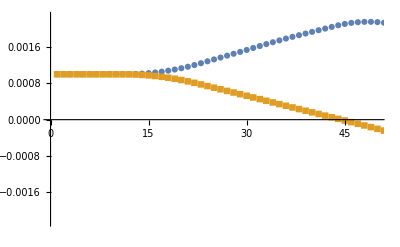

```mathematica
ListPlot[pos[[2;;,;;]],PlotRange->{{0,50},{Min[pos[[2,;;]]],Max[pos[[2,;;]]]}},PlotMarkers->Automatic]
```

```mathematica
Dimensions[MovingAverage[dat[[2,;;]],3]]
Dimensions[dat[[1,2;;-2]]]

Dimensions[MovingAverage[dat[[2,;;]],5]]
Dimensions[dat[[1,3;;-3]]]

Dimensions[MovingAverage[dat[[2,;;]],10]]
Dimensions[dat[[1,5;;-6]]]
```

{2303}

{2303}

{2301}

{2301}

{2296}

{2296}

```mathematica
zc = dat[[1,;;]];
xc3= Transpose[{dat[[1,2;;-2]],MovingAverage[dat[[2,;;]],3]}];
yc3 =Transpose[{dat[[1,2;;-2]],MovingAverage[dat[[3,;;]],3]}];

xc5= Transpose[{dat[[1,3;;-3]],MovingAverage[dat[[2,;;]],5]}];
yc5 =Transpose[{dat[[1,3;;-3]],MovingAverage[dat[[3,;;]],5]}];

xc10= Transpose[{dat[[1,6;;-5]],MovingAverage[dat[[2,;;]],10]}];
yc10 =Transpose[{dat[[1,6;;-5]],MovingAverage[dat[[3,;;]],10]}];
```

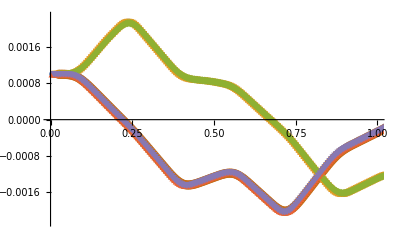

```mathematica
ListPlot[{xc3,xc5,xc10,yc3,yc5,yc10},PlotRange->{{0,1},{Min[xc3[[;;,2]]],Max[xc3[[;;,2]]]}},PlotMarkers->Automatic]
```

InterpolatingFunction::dmval: Input value {0.000234929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

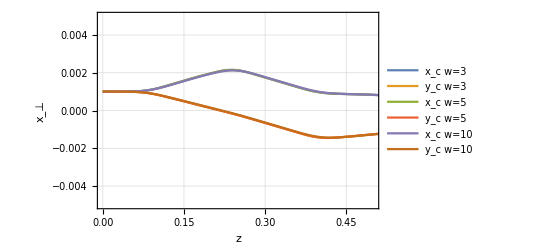

InterpolatingFunction::dmval: Input value {0.000234929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

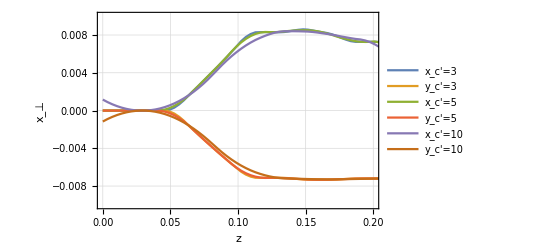

```mathematica
xcf3 = Interpolation[xc3];
ycf3 = Interpolation[yc3];

xcf5 = Interpolation[xc5];
ycf5 = Interpolation[yc5];

xcf10 = Interpolation[xc10];
ycf10 = Interpolation[yc10];

Plot[{xcf3[z],ycf3[z],xcf5[z],ycf5[z],xcf10[z],ycf10[z]},{z,0,11.5},Frame->True,FrameLabel->{Style["z",14,Bold],Style["x_⊥",14,Bold]},PlotLegends->{TextString@Row@{"x_c w=3"},TextString@Row@{"y_c w=3"},TextString@Row@{"x_c w=5"},TextString@Row@{"y_c w=5"},TextString@Row@{"x_c w=10"},TextString@Row@{"y_c w=10"}},GridLines->Automatic,BaseStyle->{FontFamily-> "Times New Roman",14},LabelStyle->{FontFamily-> "Times New Roman"},PlotRange->{{0,0.5},{-0.005,0.005}}]

Plot[{xcf3'[z],ycf3'[z],xcf5'[z],ycf5'[z],xcf10'[z],ycf10'[z]},{z,0,11.5},Frame->True,FrameLabel->{Style["z",14,Bold],Style["x_⊥",14,Bold]},PlotLegends-> {TextString@Row@{"x_c'=3"},TextString@Row@{"y_c'=3"},TextString@Row@{"x_c'=5"},TextString@Row@{"y_c'=5"},TextString@Row@{"x_c'=10"},TextString@Row@{"y_c'=10"}},GridLines->Automatic,BaseStyle->{FontFamily-> "Times New Roman",14},LabelStyle->{FontFamily-> "Times New Roman"},PlotRange->{{0,0.2},{-0.01,0.01}}]
```